# Pure Mutual Best-Response Graph

We start by creating a list of 8 bit digits to encode all possible strategy pairs.

```mathematica
bitlist={{0, 0, 0, 0, 0, 0, 0, 0}};
Do[If[Length[IntegerDigits[n, 2]]<8,AppendTo[bitlist, Join[ ConstantArray[0, 8-Length[IntegerDigits[n, 2]]], IntegerDigits[n, 2]]], AppendTo[bitlist, IntegerDigits[n, 2]]], {n, 1,255}]
```

By filling in the values for t, r, p, s, and delta one is interested in the code below produces the appropriate pmBR graph. The first block calculates the best-responses given the strategy of the opponent for each player.

```mathematica
player1BR ={};
player2BR={};
strategies={{0,0,0,0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 1}, {0, 1, 1, 0}, {1, 1, 0, 0}, {1, 0, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {0, 1, 1, 1}, {1, 0, 1, 1}, {1, 1, 0, 1}, {1, 1, 1, 0}, {1, 1, 1, 1}};
With[{r=1.0, p=0.0, t=1.5, s=-0.5, delta=3/10},Do[
bestresponse1={};
bestresponse2={};
Assuming[{Simplify[(q211>q212)Boole[strategies[[n]][[1]]==0] + (q211<q212)Boole[strategies[[n]][[1]]==1]],Simplify[(q221>q222)Boole[strategies[[n]][[2]]==0] + (q221<q222)Boole[strategies[[n]][[2]]==1]], Simplify[(q231>q232)Boole[strategies[[n]][[3]]==0] + (q231<q232)Boole[strategies[[n]][[3]]==1]],Simplify[(q241>q242)Boole[strategies[[n]][[4]]==0] + (q241<q242)Boole[strategies[[n]][[4]]==1]]},eq11 = Simplify[q111==Boole[q211>q212](p+delta Max[q111, q112])+Boole[q211<q212](t+delta Max[q121, q122])];
eq12 = Simplify[q112==Boole[q211>q212](s+delta Max[q131, q132])+Boole[q211<q212](r+delta Max[q141, q142])];
eq13 = Simplify[q121==Boole[q221>q222](p+delta Max[q111, q112])+Boole[q221<q222](t+delta Max[q121, q122])];
eq14 = Simplify[q122==Boole[q221>q222](s+delta Max[q131, q132])+Boole[q221<q222](r+delta Max[q141, q142])];
eq15 = Simplify[q131==Boole[q231>q232](p+delta Max[q111, q112])+Boole[q231<q232](t+delta Max[q121, q122])];
eq16 = Simplify[q132==Boole[q231>q232](s+delta Max[q131, q132])+Boole[q231<q232](r+delta Max[q141, q142])];
eq17 = Simplify[q141==Boole[q241>q242](p+delta Max[q111, q112])+Boole[q241<q242](t+delta Max[q121, q122])];
eq18 = Simplify[q142==Boole[q241>q242](s+delta Max[q131, q132])+Boole[q241<q242](r+delta Max[q141, q142])];
sol1 =NSolve[Rationalize[{eq11, eq12, eq13, eq14, eq15, eq16, eq17, eq18}], {q111, q112, q121, q122, q131, q132, q141, q142}];
If[sol1[[1]][[1]][[2]]>sol1[[1]][[2]][[2]], AppendTo[bestresponse1, 0]];
If[sol1[[1]][[1]][[2]]<sol1[[1]][[2]][[2]], AppendTo[bestresponse1, 1]];
If[sol1[[1]][[3]][[2]]>sol1[[1]][[4]][[2]], AppendTo[bestresponse1, 0]];
If[sol1[[1]][[3]][[2]]<sol1[[1]][[4]][[2]], AppendTo[bestresponse1, 1]];
If[sol1[[1]][[5]][[2]]>sol1[[1]][[6]][[2]], AppendTo[bestresponse1, 0]];
If[sol1[[1]][[5]][[2]]<sol1[[1]][[6]][[2]], AppendTo[bestresponse1, 1]];
If[sol1[[1]][[7]][[2]]>sol1[[1]][[8]][[2]], AppendTo[bestresponse1, 0]];
If[sol1[[1]][[7]][[2]]<sol1[[1]][[8]][[2]], AppendTo[bestresponse1, 1]];
AppendTo[player1BR, bestresponse1]
];Assuming[{Simplify[(q111>q112)Boole[strategies[[n]][[1]]==0] + (q111<q112)Boole[strategies[[n]][[1]]==1]],Simplify[(q121>q122)Boole[strategies[[n]][[2]]==0] + (q121<q122)Boole[strategies[[n]][[2]]==1]], Simplify[(q131>q132)Boole[strategies[[n]][[3]]==0] + (q131<q132)Boole[strategies[[n]][[3]]==1]],Simplify[(q141>q142)Boole[strategies[[n]][[4]]==0] + (q141<q142)Boole[strategies[[n]][[4]]==1]]},eq21 = Simplify[q211==Boole[q111>q112](p+delta Max[q211, q212])+Boole[q111<q112](t+delta Max[q231, q232])];
eq22 = Simplify[q212==Boole[q111>q112](s+delta Max[q221, q222])+Boole[q111<q112](r+delta Max[q241, q242])];
eq23 = Simplify[q221==Boole[q121>q122](p+delta Max[q211, q212])+Boole[q121<q122](t+delta Max[q231, q232])];
eq24 = Simplify[q222==Boole[q121>q122](s+delta Max[q221, q222])+Boole[q121<q122](r+delta Max[q241, q242])];
eq25 = Simplify[q231==Boole[q131>q132](p+delta Max[q211, q212])+Boole[q131<q132](t+delta Max[q231, q232])];
eq26 = Simplify[q232==Boole[q131>q132](s+delta Max[q221, q222])+Boole[q131<q132](r+delta Max[q241, q242])];
eq27 = Simplify[q241==Boole[q141>q142](p+delta Max[q211, q212])+Boole[q141<q142](t+delta Max[q231, q232])];
eq28 = Simplify[q242==Boole[q141>q142](s+delta Max[q221, q222])+Boole[q141<q142](r+delta Max[q241, q242])];
sol2 =NSolve[Rationalize[{eq21, eq22, eq23, eq24, eq25, eq26, eq27, eq28}], {q211, q212, q221, q222, q231, q232, q241, q242}];
If[sol2[[1]][[1]][[2]]>sol2[[1]][[2]][[2]], AppendTo[bestresponse2, 0]];
If[sol2[[1]][[1]][[2]]<sol2[[1]][[2]][[2]], AppendTo[bestresponse2, 1]];
If[sol2[[1]][[3]][[2]]>sol2[[1]][[4]][[2]], AppendTo[bestresponse2, 0]];
If[sol2[[1]][[3]][[2]]<sol2[[1]][[4]][[2]], AppendTo[bestresponse2, 1]];
If[sol2[[1]][[5]][[2]]>sol2[[1]][[6]][[2]], AppendTo[bestresponse2, 0]];
If[sol2[[1]][[5]][[2]]<sol2[[1]][[6]][[2]], AppendTo[bestresponse2, 1]];
If[sol2[[1]][[7]][[2]]>sol2[[1]][[8]][[2]], AppendTo[bestresponse2, 0]];
If[sol2[[1]][[7]][[2]]<sol2[[1]][[8]][[2]], AppendTo[bestresponse2, 1]];
AppendTo[player2BR,  bestresponse2]
], {n, 1, 16}]
]
```

The following block uses the best-response lists to create an edge list matching strategy pairs that are reached by mutual best-response.

```mathematica
BRgraph={};
pos1=0;
pos2=0;
Do[
player2={bitlist[[n]][[1]], bitlist[[n]][[2]], bitlist[[n]][[3]], bitlist[[n]][[4]]};
player1={bitlist[[n]][[5]], bitlist[[n]][[6]], bitlist[[n]][[7]], bitlist[[n]][[8]]};
bestresponsevec = {player1BR[[Position[strategies, player1][[1]][[1]]]][[1]], player1BR[[Position[strategies, player1][[1]][[1]]]][[2]], player1BR[[Position[strategies, player1][[1]][[1]]]][[3]], player1BR[[Position[strategies, player1][[1]][[1]]]][[4]], player2BR[[Position[strategies, player2][[1]][[1]]]][[1]], player2BR[[Position[strategies, player2][[1]][[1]]]][[2]], player2BR[[Position[strategies, player2][[1]][[1]]]][[3]], player2BR[[Position[strategies, player2][[1]][[1]]]][[4]]};
AppendTo[BRgraph, n-> Position[bitlist, bestresponsevec][[1]][[1]]], {n, 1, 256}]
```

The following line plots the graph.

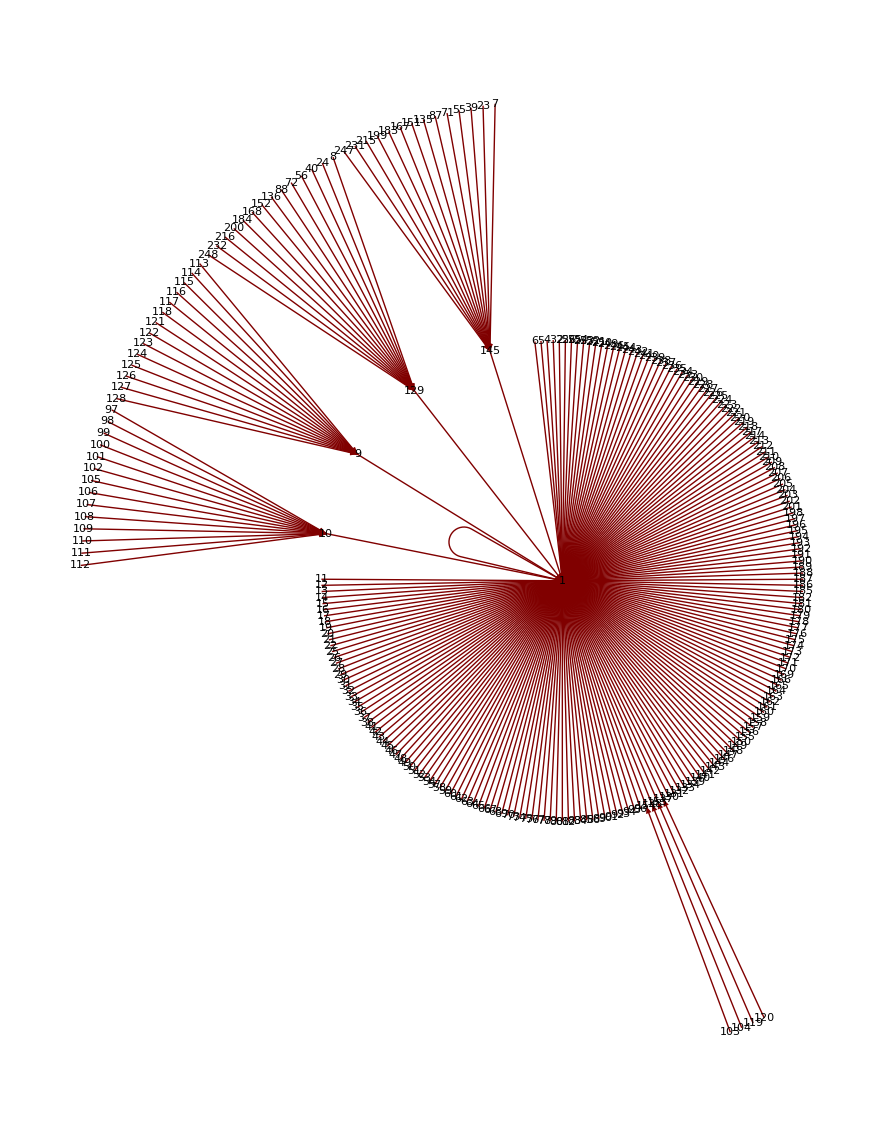

```mathematica
GraphPlot[BRgraph, VertexLabeling->True, DirectedEdges->True]
```

The edge list can be printed by executing the following.

```mathematica
BRgraph
```

{1→1,2→1,3→1,4→1,5→1,6→1,7→145,8→129,9→1,10→1,11→1,12→1,13→1,14→1,15→1,16→1,17→1,18→1,19→1,20→1,21→1,22→1,23→145,24→129,25→1,26→1,27→1,28→1,29→1,30→1,31→1,32→1,33→1,34→1,35→1,36→1,37→1,38→1,39→145,40→129,41→1,42→1,43→1,44→1,45→1,46→1,47→1,48→1,49→1,50→1,51→1,52→1,53→1,54→1,55→145,56→129,57→1,58→1,59→1,60→1,61→1,62→1,63→1,64→1,65→1,66→1,67→1,68→1,69→1,70→1,71→145,72→129,73→1,74→1,75→1,76→1,77→1,78→1,79→1,80→1,81→1,82→1,83→1,84→1,85→1,86→1,87→145,88→129,89→1,90→1,91→1,92→1,93→1,94→1,95→1,96→1,97→10,98→10,99→10,100→10,101→10,102→10,103→154,104→138,105→10,106→10,107→10,108→10,109→10,110→10,111→10,112→10,113→9,114→9,115→9,116→9,117→9,118→9,119→153,120→137,121→9,122→9,123→9,124→9,125→9,126→9,127→9,128→9,129→1,130→1,131→1,132→1,133→1,134→1,135→145,136→129,137→1,138→1,139→1,140→1,141→1,142→1,143→1,144→1,145→1,146→1,147→1,148→1,149→1,150→1,151→145,152→129,153→1,154→1,155→1,156→1,157→1,158→1,159→1,160→1,161→1,162→1,163→1,164→1,165→1,166→1,167→145,168→129,169→1,170→1,171→1,172→1,173→1,174→1,175→1,176→1,177→1,178→1,179→1,180→1,181→1,182→1,183→145,184→129,185→1,186→1,187→1,188→1,189→1,190→1,191→1,192→1,193→1,194→1,195→1,196→1,197→1,198→1,199→145,200→129,201→1,202→1,203→1,204→1,205→1,206→1,207→1,208→1,209→1,210→1,211→1,212→1,213→1,214→1,215→145,216→129,217→1,218→1,219→1,220→1,221→1,222→1,223→1,224→1,225→1,226→1,227→1,228→1,229→1,230→1,231→145,232→129,233→1,234→1,235→1,236→1,237→1,238→1,239→1,240→1,241→1,242→1,243→1,244→1,245→1,246→1,247→145,248→129,249→1,250→1,251→1,252→1,253→1,254→1,255→1,256→1}